```mathematica
(* Rational parametrization *)
sol=Table[{
y0->-(1-t^2)/(1+t^2),
x0->(2t)/(1+t^2)
},{t,-2,2,1/8} ];
vf={-x^3, -y^3+x};

lines=({-x0,-y0}.({x,y}-{x0,y0}))>=0/.sol ;
approximation=And@@lines;
```

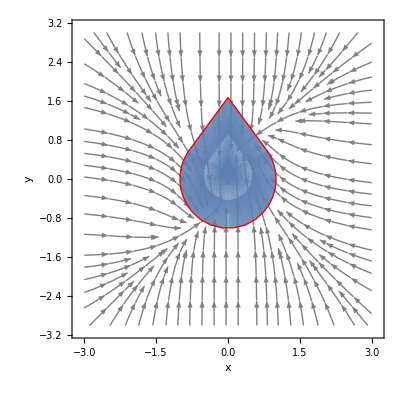

```mathematica
ℛ=ImplicitRegion[approximation,{x,y}];

Show[
StreamPlot[vf,{x,-3,3},{y,-3,3},
 StreamStyle->Gray,
FrameLabel->{
Style[TraditionalForm[x],18, Black], 
Style[TraditionalForm[y],18, Black]},
LabelStyle->{FontFamily->"Source Serif Pro"},
 FrameTicks->Automatic,
 PlotRangePadding->0],
RegionPlot[BoundaryDiscretizeRegion[ℛ,MaxCellMeasure->{"Length"->0.02}], 
BoundaryStyle->{Thick, Red}
]
]
```

```mathematica
ES`ContinuousInvariantQ[approximation,vf, {x,y},True]//Timing
```

{0.161711,False}

```mathematica
LZZ`ContinuousInvariantQ[approximation,vf, {x,y},True]//Timing
```

$Aborted